# 25: Eigenvalue Algorithms:

We know that we can not use the Characteristic Polynomial to compute eigenvalues. The question is how do we compute all the eigenvalues or more generally the eigen decomposition of a matrix A.

We are going to find out one way to compute roots of polynomials.

## Companion Polynomials

Matlab computes polynomial roots by building a matrix which has the same roots.  There are actually a whole bunch of these companion matrices for a given polynomial. The most common is implemented below

```mathematica
CompanionMatrix[a_]:= Module[{m=Length[a],A},
A=SparseArray[{Band[{2,1}]->1},{m-1,m-1}];
A⟦All,m-1⟧=-a⟦1;;-2⟧/a⟦-1⟧;
A
]
```

```mathematica
p[x_]:=2. x^2+3x +1 + x^7+π x^6
a=CoefficientList[p[x], x]
A=CompanionMatrix[a];
MatrixForm[A]
Sort[Eigenvalues[N[A]]]
Sort[x/.NSolve[p[x]==0,x]]
```

{1,3,2.,0,0,0,π,1}

```mathematica
Eigenvalues[A]
Solve[p[x]==0,x]
```

{-3.15322+0. ⅈ,0.864539+0.620724 ⅈ,0.864539-0.620724 ⅈ,-0.301024+0.891854 ⅈ,-0.301024-0.891854 ⅈ,-0.557703+0.0704326 ⅈ,-0.557703-0.0704326 ⅈ}

{{x→-3.15322},{x→-0.557703-0.0704326 ⅈ},{x→-0.557703+0.0704326 ⅈ},{x→-0.301024-0.891854 ⅈ},{x→-0.301024+0.891854 ⅈ},{x→0.864539-0.620724 ⅈ},{x→0.864539+0.620724 ⅈ}}

```mathematica
m=5;
Dir3PtMat=SparseArray[{Band[{1,1}]->-2.0, Band[{1,2}]->1.0,Band[{2,1}]->1.0},{m,m}];
Per3PtMat=Dir3PtMat; Per3PtMat⟦1,m⟧=Per3PtMat⟦m,1⟧=1.0;
Map[MatrixForm,{Dir3PtMat,Per3PtMat}]
```

{(-2. | 1. | 0 | 0 | 0
1. | -2. | 1. | 0 | 0
0 | 1. | -2. | 1. | 0
0 | 0 | 1. | -2. | 1.
0 | 0 | 0 | 1. | -2.),(-2. | 1. | 0 | 0 | 1.
1. | -2. | 1. | 0 | 0
0 | 1. | -2. | 1. | 0
0 | 0 | 1. | -2. | 1.
1. | 0 | 0 | 1. | -2.)}

For the 5627 Project ILU0 code you might need to get the pieces of a sparse Array.  The last entry here just says that everything else is a zero.

```mathematica
Hmm=ArrayRules[Per3PtMat]
```

{{1,2}→1.,{1,1}→-2.,{1,5}→1.,{2,1}→1.,{2,3}→1.,{2,2}→-2.,{3,2}→1.,{3,4}→1.,{3,3}→-2.,{4,4}→-2.,{4,5}→1.,{4,3}→1.,{5,4}→1.,{5,5}→-2.,{5,1}→1.,{_,_}→0}

```mathematica
?SparseArray
```

## Theorem 25.1: Galois

We all know the quadratic formula for the roots of a λ^2+b λ+c =0. There is a formula for the three roots of a cubic.  Here is one version!

```mathematica
Clear[a,b,c,λ]
λ/.Solve[λ^3+a λ^2+b λ+c==0,λ]
```

{-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}

There is a much longer formula for the four roots of a quartic

```mathematica
Clear[a,b,c,d,λ]
λ/.Solve[λ^4+a λ^3+b λ^2+c λ +d==0,λ]
```

{-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))))}

Abel proved in 1824 that no such general formula can exist for higher degree polynomials!  See Theorem 25.1 for a careful statement of the theorem. What this means is that algorithms to compute eigenvalues need to be iterative like Newton’s method!

Computing eigenvalues using the characteristic polynomial is a bad idea because it would be unstable.  But it is even worse, Abel’s result means that there is no formula for non-tiny matrices.

## Iterative Schemes

Iterative schemes have some advantages

Black-box algorithms only use the matrix rather than work on the matrix.  This is essential to exploit sparsity! It also means they do not need to compute all the eigenvalues. Maybe you only care about the big ones!

You do not have to wait for full convergence if a “rough” answer will do.

Here is another iterative eigenvalue algorithm.  The power method one very different from Jacobi: Jacobi finds all the eigenvalues by operating on the matrix while the power method finds one particular eigenvalue by using the matrix.

### Power Method: A Simple Iterative Scheme

There is a simple way to compute the eigenvector associated with the largest eigenvalue of almost any matrix A. In words, multiply by A and normalize repeatedly.  This is very easy to code.

```mathematica
PowerMethod[A_][x_]:=Module[{z=A.x},z/Norm[z]]
```

It works!  Here is a simple test on an SPD matrix.

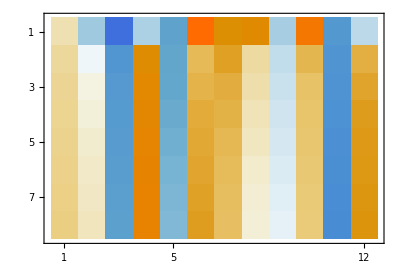

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,7];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

It has almost converged to the eigenvector associated with the largest eigenvalue!

```mathematica
{{λ},{v}}=Eigensystem[A,1]
```

{{9.73284},{{0.185846,0.0480755,-0.383134,0.459296,-0.27367,0.341196,0.246871,0.0106236,-0.0244387,0.202752,-0.452704,0.326176}}}

```mathematica
vv=PowerMethodData⟦-1⟧
(A.vv)/vv
```

{0.185827,0.0477241,-0.390512,0.457077,-0.280117,0.323141,0.244351,0.0235551,-0.0385214,0.219719,-0.444974,0.332957}

{9.74747,9.9845,9.68981,9.74253,9.65119,9.85425,9.70354,8.36093,9.01733,9.62569,9.75848,9.71985}

```mathematica
{18.782680833027204,18.78267992377554,18.782691955769128,18.782640469938702,18.782677319405842,18.78266970926498,18.782679702106222,18.782671252773063,18.782688903488058,18.782674831333594,18.78267562671868,18.782684167730785,18.78267199699047,18.782672394627376,18.78267214569421,18.782682632835648}
```

It also works more generally! Here it is on a general symmetric matrix.

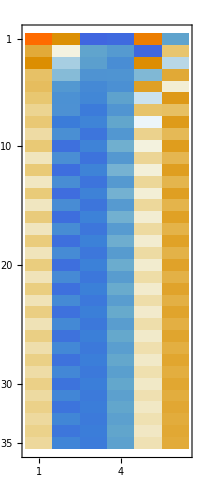

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

It also frequently (but not always) works on a general matrix.

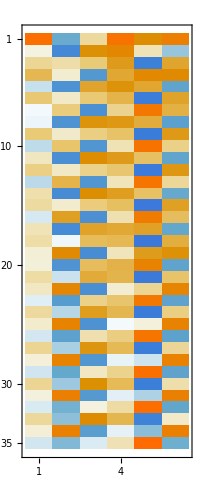

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

```mathematica
Eigenvalues[A]
```

```mathematica
vEnd=PowerMethodData⟦-3;;-1⟧
```

## Preliminary Hessenberg Reduction

For now we are going to look at classical dense matrix eigenvalue algorithms which start with a reduction very similar to a QR decomposition and then iterates to reveal all the eigenvalues of a dense matrix.

We are going to look and see what the first step does before we learn how to do it!

### Symmetric Matrix⟶Tri-Diagonal⟶^(k→∞)Diagonal

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,T}=HessenbergDecomposition[A];
TabView[{"A"->MatrixPlot[A],"T"->MatrixPlot[T],"Q"->MatrixPlot[Q]}]
Map[Norm,{T-Qᵀ.A.Q,A-Q.T.Qᵀ,Q.Qᵀ-IdentityMatrix[m],Eigenvalues[A]-Eigenvalues[T]}]
TabView[{"A"->GershgorignPic[A],"T"->GershgorignPic[T]}]
```

123

{2.11379×10^-15,3.42175×10^-15,1.0549×10^-15,9.76937×10^-15}

12

The tridiagonal matrix give tighter bounds. If we could make it more diagonal we would be able to isolate the eigenvalues.  This is the plan.  For symmetric matrices we are going to work out how to make the tridiagonal matrix more diagonal.

### General Matrix⟶Almost Upper Triangular⟶^(k→∞)UT

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; 
{Q,H}=HessenbergDecomposition[A];
TabView[{"A"->MatrixPlot[A],"H"->MatrixPlot[H],"Q"->MatrixPlot[Q]}]
Map[Norm,{H-Qᵀ.A.Q,A-Q.H.Qᵀ,Qᵀ.Q-IdentityMatrix[m],Eigenvalues[A]-Eigenvalues[H]}]
TabView[{"A"->GershgorignPic[A],"H"->GershgorignPic[H]}]
```

123

{1.7338×10^-15,4.50029×10^-15,8.62333×10^-16,8.73697×10^-15}

12

The almost upper triangular matrix give tighter bounds. If we could make it more upper triangular we would be able to isolate the eigenvalues.  This is the plan.  For general matrices we are going to work out how to make the almost upper triangular matrix more upper triangular.

## Localization “GershgorignPic” Code (From Earlier)

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r1,r2},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```